# 3. izpit – Mathematica

## Računalniški praktikum 2024/25

Študijska smer : Finančna matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

V tem delu izpita sta dve nalogi, ki sta skupaj vredni 32 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.

## 1. naloga [12 točk]

1. (4 točke) Izračunajte limito lim_(z→1+i) (z^4.-1)/(z^2-1)
2. (4 točke) Izračunajte določeni integral funkcije  x^2 sin(x) na intervalu [0,].
3. (4 točke) Poiščite vsa taka cela števila m in n, da bo veljalo 42 m+2025 n==3. 
Iskanje rešitev v celih številih lahko določite z dodatnim parametrom Integers.

```mathematica
Limit[(z^4-1)/(z^2-1),z->1+I]
Integrate[x^2Sin[x],{x,0,Pi}]
Solve[42*m+2019*n==3,{m,n},Integers]
```

1+2 ⅈ

-4+π^2

{{m→ConditionalExpression[625+673 C[1], C[1]∈ℤ],n→ConditionalExpression[-13-14 C[1], C[1]∈ℤ]}}

## 2. naloga [20 točk]

1. (5 točk) Definirajte funkciji f(x)=x^2-x in g(x)=(4-x)/(x^2-6x+9).
2. (5 točk) Izračunajte vrednost x, pri kateri funkcija f doseže minimum.
3. (5 točk) Na eno sliko narišite grafa funkcij na intervalu [-2,2].
4. (5 točk) Numerično izračunajte vrednosti x, pri katerih se grafa funkcij f in g na intervalu [-2,2] sekata.
Izračunajte še y koordinate presečišč..

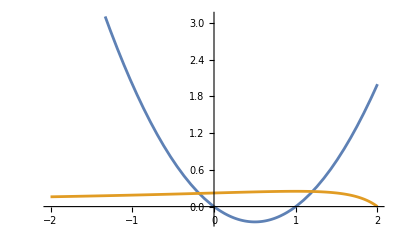

{{x→-0.182271},{x→1.2048}}

{{x→1/2}}

```mathematica
f[x_]:=x^2-x
g[x_]:=(2-x)/(x^2-6x+9)
Plot[{f[x],g[x]},{x,-2,2}]
NSolve[f[x]==g[x],x,Reals]
Solve[f'[x]==0]
```